```mathematica
Le=LessEqual; Ge=GreaterEqual; Eq=Equal;
```

```mathematica
pre1=Module[{},
Or[And[Ge[x,0],Le[x,0.5],Ge[y,0],Le[y,0.5]],
And[Le[x,1],Ge[x,0],Le[x,0.5],Ge[y,0],Le[y,0.5]]]]//FullSimplify//LogicalExpand
```

x≥0&&y≥0&&x≤0.5&&y≤0.5

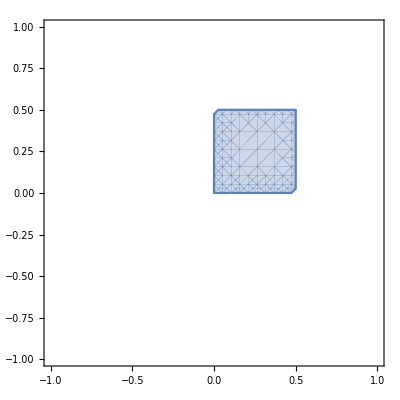

```mathematica
RegionPlot[pre1,{x,-1,1},{y,-1,1}]
```

```mathematica
pre2=Module[{},
And[Le[x,1.0],Eq[y,0],Ge[x,-0.70710678118],Le[x,0]]]//FullSimplify//LogicalExpand
```

y==0&&-0.707107≤x&&x≤0

```mathematica
RegionPlot[pre2,{x,-1,1},{y,-1,1}]
```

-Graphics-

```mathematica
pre3=Module[{},
And[Le[x,1],
Eq[y,0],
Ge[x,-0.707107],
Le[x,0],
Le[y,0],
Ge[y,-0.707107],
Le[x,0.707107]]]//FullSimplify//LogicalExpand
```

y==0&&-0.707107≤x&&x≤0

```mathematica
RegionPlot[pre3,{x,-1,1},{y,-1,1}]
```

-Graphics-

```mathematica
pre4=Module[{a1,a2},
a1=And[Le[x,0.5],Le[y,0.5],Ge[x,0],Ge[y,0]];
a2=And[Or[And[Ge[x,0],Le[x,0.5],Ge[y,0],Le[y,0.5]],
Le[x,1]],
Or[And[Eq[y,0],Le[0,x],Le[x,0.707107]],a1]];
Or[a1,a2]]//FullSimplify//LogicalExpand
```

(y==0&&x≥0&&x≤0.707107)||(x≥0&&y≥0&&x≤0.5&&y≤0.5)

```mathematica
RegionPlot[pre4,{x,-1,1},{y,-1,1}]
```

-Graphics-

```mathematica
pre5=Module[{},
And[Le[x,1],
Or[And[Ge[x,0],Le[x,0.5],Ge[y,0],Le[y,0.5]],
And[Eq[y,0],Ge[x,-0.707107],Le[x,0]]]]]//FullSimplify//LogicalExpand
```

(y==0&&-0.707107≤x&&x≤0)||(0≤x&&0≤y&&x≤0.5&&y≤0.5)

```mathematica
RegionPlot[pre5,{x,-1,1},{y,-1,1}]
```

-Graphics-

```mathematica
pre6=Module[{},
And[Le[x,1],
Eq[y,0],
Ge[x,-0.707107],
Le[x,0],
Le[y,0],
Ge[y,-0.707107],
Le[x,0.707107],
Or[And[Ge[x,0],Le[x,0.5],Ge[y,0],Le[y,0.5]],
And[Eq[y,0],Ge[x,-0.707107],Le[x,0]]]]]//FullSimplify//LogicalExpand
```

y==0&&-0.707107≤x&&x≤0

```mathematica
RegionPlot[pre6,{x,-1,1},{y,-1,1}]
```

-Graphics-

```mathematica
pre7=Module[{a1,a2},
a1=And[Le[x,0.5],Le[y,0.5],Ge[x,0],Ge[y,0]];
a2=And[Or[a1,Le[x,1]],
Or[And[Eq[y,0],Le[0,x],Le[x,0.707107]],a1]];
Or[a1,a2]]//FullSimplify//LogicalExpand
```

(y==0&&x≥0&&x≤0.707107)||(x≥0&&y≥0&&x≤0.5&&y≤0.5)

```mathematica
RegionPlot[pre7,{x,-1,1},{y,-1,1}]
```

-Graphics-

```mathematica
pre8=Module[{},
And[Le[x,1],
Eq[y,0],
Ge[x,-0.707107],
Le[x,0]]]//FullSimplify//LogicalExpand
```

y==0&&-0.707107≤x&&x≤0

```mathematica
RegionPlot[pre8,{x,-1,1},{y,-1,1}]
```

-Graphics-

```mathematica
inv1=Module[{a1,a2,a3},
a1=And[Le[x,0.5],Le[y,0.5],Ge[x,0],Ge[y,0]];
a2=Or[And[Eq[y,0],Le[0,x],Le[x,0.707107]],a1];
a3=And[Or[And[Ge[x,0],Le[x,0.5],Ge[y,0],Le[y,0.5]],
Le[x,1]],
a2];
Or[a1,And[Or[a1,a3],a2]]]//FullSimplify//LogicalExpand
```

(y==0&&x≥0&&x≤0.707107)||(x≥0&&y≥0&&x≤0.5&&y≤0.5)

```mathematica
RegionPlot[inv1,{x,-1,1},{y,-1,1}]
```

-Graphics-

```mathematica
inv2=Module[{},
And[Le[x,1],
Eq[y,0],
Ge[x,-0.707107],
Le[x,0],
Le[y,0],
Ge[y,-0.707107],
Le[x,0.707107],
Or[And[Ge[x,0],Le[x,0.5],Ge[y,0],Le[y,0.5]],
And[Eq[y,0],Ge[x,-0.707107],Le[x,0]]]]]//FullSimplify//LogicalExpand
```

y==0&&-0.707107≤x&&x≤0

```mathematica
RegionPlot[inv2,{x,-1,1},{y,-1,1}]
```

-Graphics-